```mathematica
Needs["ErrorBarPlots`"]
SetOptions[$FrontEndSession,PrintPrecision->10]
(*----------------------------------------------------------------------------------*)
(*The datafile must be in the format: {{Beta, Kurtosis, ErrorKurtosis}}*)
DataNs1=Import["/home/sciarra/Script/CollapsePlot/Mathematica/muiPiT_mass5500_nt6_ns18.dat"];
DataNs2=Import["/home/sciarra/Script/CollapsePlot/Mathematica/muiPiT_mass5000_nt6_ns24.dat"];
DataNs3=Import["/home/sciarra/Script/CollapsePlot/Mathematica/muiPiT_mass5000_nt6_ns30.dat"];
DataNs4=Import["/home/sciarra/Script/CollapsePlot/Mathematica/muiPiT_mass5000_nt6_ns36.dat"];
Ns1=18;
Ns2=24;
Ns3=30;
Ns4=36;
Data1={DataNs1,Ns1};
Data2={DataNs2,Ns2};
Data3={DataNs3,Ns3};
Data4={DataNs4,Ns4};
bCmin=5.80; bCmax=bCmin; bCres=0.1;
nuMin=0.25; nuMax=0.85; nuRes=0.01;
(*----------------------------------------------------------------------------------*)
(*Some auxiliary later assignments*)
xMap[b_,bC_,ns_,nu_]:=(b-bC)*ns^(1/nu);
x[data_,bC_,nu_]:=xMap[data[[1]][[All,1]],bC,data[[2]],nu];
xRangeCalc[data1_,data2_,bC_,nu_]:={Max[{x[data1,bC,nu][[1]],x[data2,bC,nu][[1]]}],Min[{x[data1,bC,nu][[-1]],x[data2,bC,nu][[-1]]}]};
kurtosis[data_,bC_,nu_]:=Transpose[{x[data,bC,nu],data[[1]][[All,2]]}];
kurtosisError[data_,bC_,nu_]:=Transpose[{x[data,bC,nu],data[[1]][[All,3]]}];
ProduceCollapseQualityPlot[list_]:=ErrorListPlot[Table[{{list[[i,2]],list[[i,3]]},ErrorBar[list[[i,4]]]},{i,Dimensions[list][[1]]}],AxesOrigin->{0.2,0}, PlotRange->All];
```

```mathematica
(*Test considering fake data from f(β)=β^2 and g(β)=β-2 with β∈[1,3], Ns=1, ν=1 and Subscript[β, c]=2.
Therefore: x=β-2, namely β=x+2, x∈[-1,1] and f(x)=(x+2)^2 and g(x)=x.
 The distance is √(1/2∫_-1^1 (f(x)-g(x))^2 ⅆx) = 2 √(82/15)≃ 4.676180778*)
TestBetaSquared=Import["/home/sciarra/Script/CollapsePlot/Mathematica/Test_betaSquared.dat"];
TestBetaMinusTwo= Import["/home/sciarra/Script/CollapsePlot/Mathematica/Test_betaMinusTwo.dat"];
betaCtest=2;
nuTest=1;
TestData1={TestBetaSquared,nuTest};
TestData2={TestBetaMinusTwo,nuTest};
kurtosisTest1=Interpolation[kurtosis[TestData1,betaCtest, nuTest]];
kurtosisTest2=Interpolation[kurtosis[TestData2,betaCtest, nuTest]];
Sqrt[0.5*N[Integrate[(kurtosisTest1[x]-kurtosisTest2[x])^2,{x,-1,1}]]]==N[2Sqrt[82/15]]
```

True

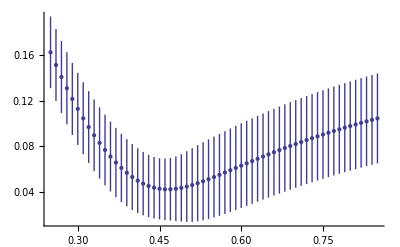

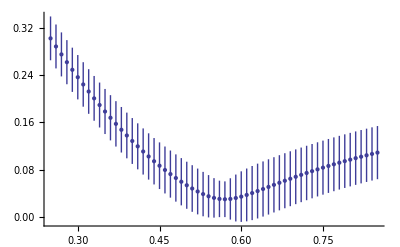

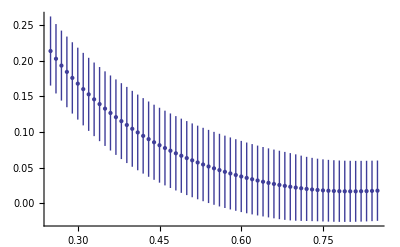

```mathematica
(*Start with an empty table and fill it row after row*)
Clear[listOfPlots]
listOfPlots={};
Do[
If[data1[[2]]>=data2[[2]],Continue[]];
collapseQualityScan={};
Do[
xRange=xRangeCalc[data1,data2,bC,nu];
(*Here the data are reorganised for the interpolation and they are interpolated*)
k1=Interpolation[kurtosis[data1,bC,nu]];
k2=Interpolation[kurtosis[data2,bC,nu]];
kErr1=Interpolation[kurtosisError[data1,bC,nu]];
kErr2=Interpolation[kurtosisError[data2,bC,nu]];
(*Now the distance can be calculated and the error on it as well propagating
ERROR PROPAGATION: h=(f-g)^2
	           sigma_h=sqrt[(de_h/de_f)^2*sigma_f^2+(de_h/de_g)^2*sigma_g^2]
                      =2*|f-g|*sqrt(sigma_f^2+sigma_g^2)
*)
kDistanceSquared=N[Integrate[(k1[x]-k2[x])^2,{x,xRange[[1]],xRange[[2]]}]];
kDistanceErrSquared=N[Integrate[2*Abs[k1[x]-k2[x]]*Sqrt[(kErr1[x])^2+(kErr2[x])^2],{x,xRange[[1]],xRange[[2]]}]];
(*We are now ready to perform the integration. Here we will need a small further error propagation when we
divide by the integration interval width and we take the square root.
d=sqrt(I/a) => sigma_d=sigma_I/(2*sqrt(a*I))
*)
collapseQuality={bC,nu,Sqrt[kDistanceSquared/(xRange[[2]]-xRange[[1]])],kDistanceErrSquared/Sqrt[4*(xRange[[2]]-xRange[[1]])*kDistanceSquared]};
AppendTo[collapseQualityScan,collapseQuality];
Clear[xRange,k1,k2,kErr1,kErr2,kDistanceSquared,kDistanceErrSquared,collapseQuality]
 ,{bC,bCmin,bCmax,bCres}
,{nu,nuMin,nuMax,nuRes}]
AppendTo[listOfPlots,ProduceCollapseQualityPlot[collapseQualityScan]]
Clear[collapseQualityScan]
,{data1,{Data2,Data3,Data4}},{data2,{Data2,Data3,Data4}}]

Do[listOfPlots[[i]]//Print,{i,Length[listOfPlots]}]
```

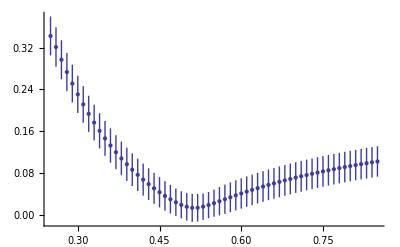

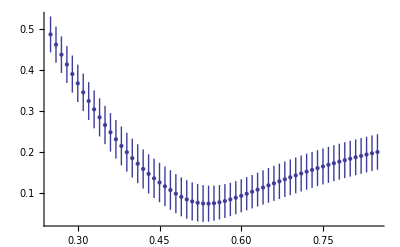

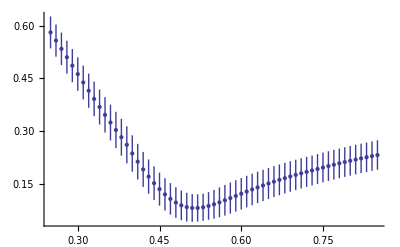

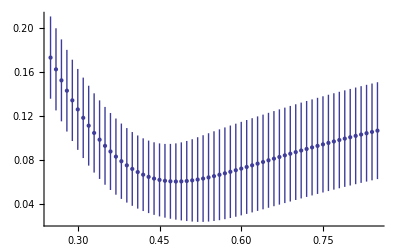

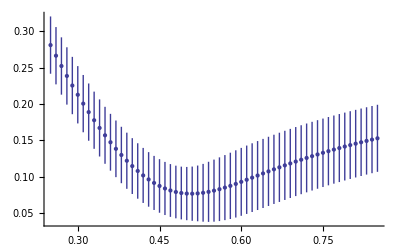

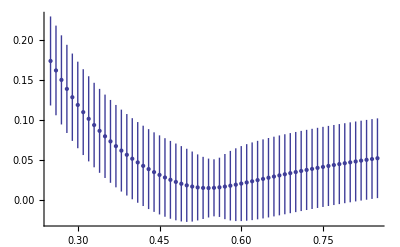

```mathematica
(*mass5500*)
```

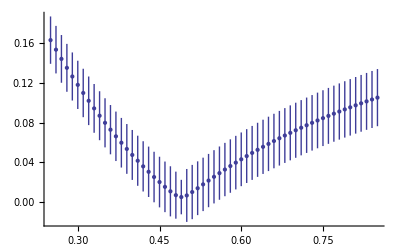

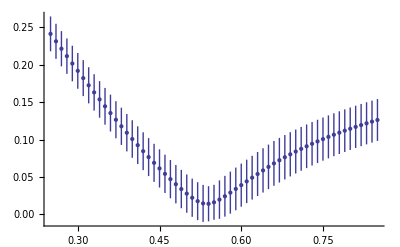

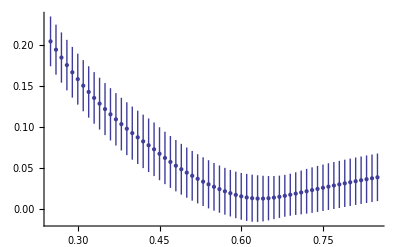

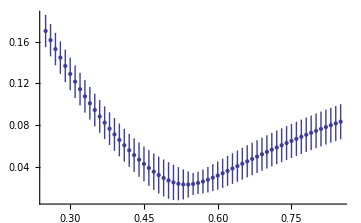
(*mass6500*)
-Graphics-

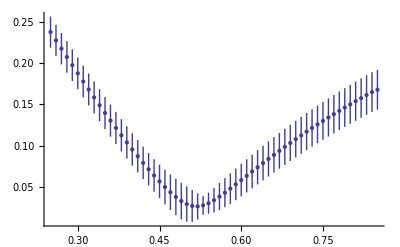

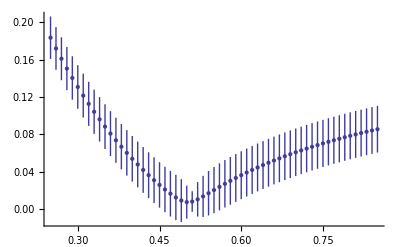

```mathematica
(*mass4500*)
```